```mathematica
f[x_]=(x^3-3 x +1)/(x^2-x)-1.5
```

```mathematica
f'[x]
```

```mathematica
Solve[f'[x]==0,x]
```

```mathematica
Table[N[f[ⅇ^((2π n ⅈ)/6)]],{n,6}]
```

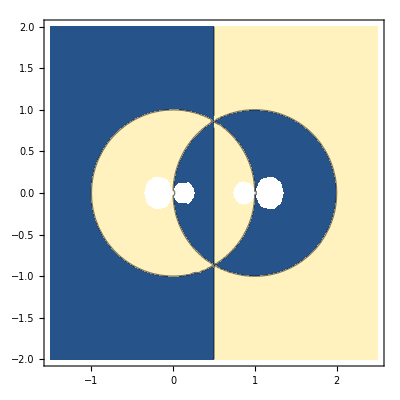

```mathematica
ContourPlot[Re[f[x+ ⅈ y]],{x,-1.5,2.5},{y,-2,2}, Contours->{0}]
```